```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\reimplementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
pnData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,pnData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractPnData[ds_,directive_,keys_,which_:{1}]:=Module[
{data,x,y,result},
data=Apply[ds,directive];
x=Table[i,{i,0,-1+((data[Take,keys[[1]]]//Normal)[[1]]//Length)}];
y=(data[Take,keys[[2]]]//Normal)[[1]];
result={};
If[Depth[y]==2,result={Table[{x[[it]],y[[it]]},{it,Length[x]}]},
Do[(
pn=y[[i]];
AppendTo[result,Table[{x[[it]],pn[[it]]},{it,Length[x]}]];
),{i,which}]];
Return[result]
]
```

```mathematica
getPlot[data_,k_:0]:=(
SetOptions[LinTicks,TickLengthScale->2.5];

color = Blue;
expl=16;
inplt = ListPlot[data,
PlotRange->{{4,28},{10^-expl,0.3001}},ImageSize->240,
Frame->True,Axes->False,
FrameStyle->Directive[Black,10,FontFamily->"Bookman Old Style"],
PlotMarkers->{"●", 8},
Joined->False,
FrameLabel->{Style["n",Black,12,FontFamily->"Bookman Old Style"],Style["-log_10P_n",Black,12,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,12],
PlotStyle->color,
AspectRatio->0.8,
FrameTicks->{{Table[{10^-n,n},{n,2,expl,2}],None},Automatic},
ScalingFunctions->"Log"];

plt=ListPlot[data,
PlotRange->{Full,{0,0.3001}},ImageSize->240,
Frame->True,Axes->False,
FrameStyle->Directive[Black,18,FontFamily->"Bookman Old Style"],
PlotMarkers->{"●", 8},
Joined->False,
Epilog->{Text[
Style["(b)  λ = 0",Black,20,FontFamily->"Bookman Old Style"],
{7,0.26}],
Inset[inplt,{10.5,0.22},{0,0.3},20]},
FrameLabel->{Style["n",Black,20,FontFamily->"Bookman Old Style"],Style["P_n",Black,20,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,20],
PlotStyle->color,
AspectRatio->.75,
FrameTicks->{{LinTicks[0, 0.3, 0.1, 5],StripTickLabels[LinTicks[0, 0.3, 0.1, 5]]},{LinTicks[0,pnAvail["size"][[1]],4,4],StripTickLabels[LinTicks[0,pnAvail["size"][[1]],4,4]]}}
];

Show[plt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsPn[key_, which_:{1}]:=Module[
{plots,directive,keys,pn},
directive={Select[#coupling==J&&#interaction==B&]};
keys={"momentum",key};

plots={};
Do[(
Do[(
pn=extractPnData[pnDataset,directive,keys,which];
Do[
AppendTo[plots,getPlot[pn[[j]],which[[j]]-1]];
,{j,Length[which]}];
),{B,pnAvail["interaction"]//Normal}];
),{J,pnAvail["coupling"]//Normal}];

Return[plots]
];
```

```mathematica
SavePlots[plots_,offset_]:=(
For[it=1,it≤Length[plots],it++,(
filename=StringJoin["../implementation/plots/pn/pn_",StringPadLeft[ToString[offset+it],4,"0"],".png"];
Export[filename,plots[[it]]];
)];
)
```

J ∈ {0.4} @ 28-2-28_0.0-1.0-1.0

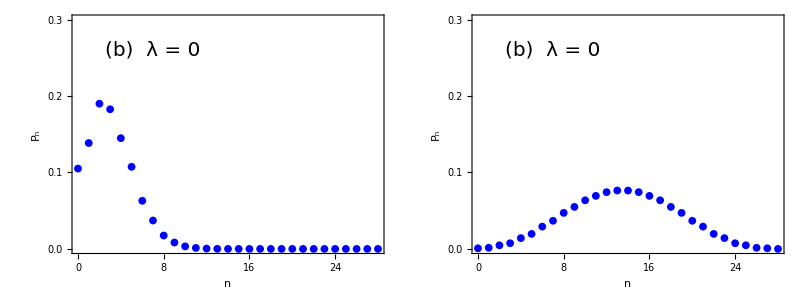

```mathematica
JRange={"0.4"};
tails={"28-2-28_0.0-1.0-1.0"};
pnPlots={};
Do[(
pnDataset=Dataset[getAssoc["pn",JRange,tail]];
pnAvail=Dataset[getStruct[pnDataset]];
Print[Style[StringJoin["J ∈ ",ToString[JRange]," @ ", tail],16]];
AppendTo[pnPlots,makePlotsPn["P1n",{1+pnAvail["size"][[1]]/4}]];
Print[Grid[pnPlots]];
),{tail,tails}]
```

```mathematica
(*SavePlots[pnPlots[[1]],0]*)
```